# 3강 함수와 그래프

전경원<ruddyscent@gmail.com>

2014년 9월 2일 화요일

## 함수 정의하기

#### 함수를 정의하는 방법

함수 이름은 반드시 소문자로 시작하도록 정한다. 매스매티카 내장 함수의 이름은 대분자로 시작하므로 내장 함수 이름과 충돌하는 일을 방지할 수 있다.

함수 정의의 왼쪽에 있는 매개변수에 언더스코어를 붙인다.

함수의 매개변수는 [과 ]로 둘러싼다.

함수 정의의 왼쪽과 오른쪽은 :=로 연결한다.

### 함수 삭제하기

## 그래프 그리기

### 실습

다음 함수를 -10≤x≤10 범위에서 그래프를 그려보세요.

Sin(1+Cos(x))

Sin(1.4+Cos(x))

Sin(π/2+Cos(x))

Sin(2+Cos(x))

## Plot 함수의 옵션

#### 실습

그래프를 이용하여 x=2에서의 함수 f(x)=√x 근삿값을 찾아보세요.

### 두 축에 동일 비율을 사용하려면

### 두 축이 원점을 교차하도록 하려면

### 매시 포인트을 보려면

### 색과 스타일을 바꾸려면

### 좌표축을 없애고 테두리를 넣으려면

#### 실습

Axes, Frame, Filling, FrameStyle, PlotRange, AspectRatio 등의 옵션을 사용하여 y=Cos(15x)/(1+x^2)의 그래프를 다음과 같이 그려보세요.

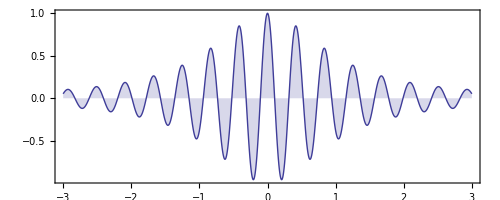

### 축에 화살표를 사용하려면

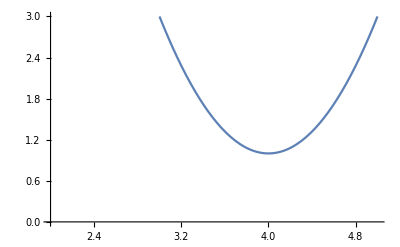

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesOrigin->{2,0}]
```

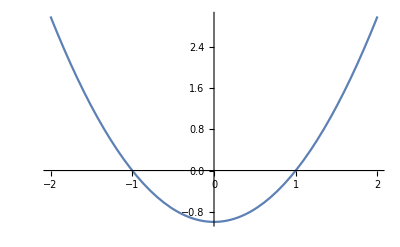

```mathematica
Plot[x^2-1,{x,-2,2}]
```

### 격자를 사용하려면

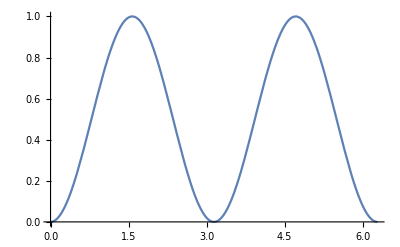

```mathematica
Plot[Sin[x]^2,{x,0,2π}]
```

### 좌표축의 눈금을 조정하려면

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLinesStyle->Lighter[Gray],GridLines->{Range[0,2π,π/8],Range[0,1,.1]}]
```

-Graphics-

#### 실습

다음 그래프와 같이 사인 그래프를 그려보세요.

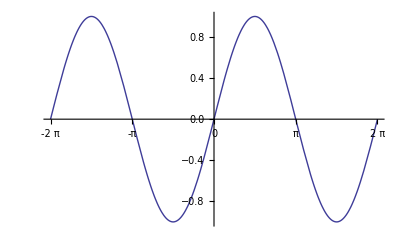

### 라벨을 추가하려면

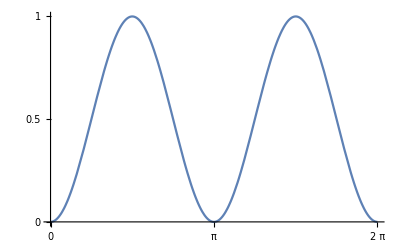

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}}]
```

### 제외와 수직 점근선

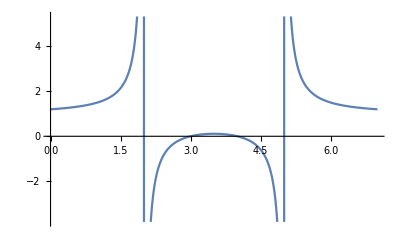

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7}]
```

### 로그 비율을 사용하려면

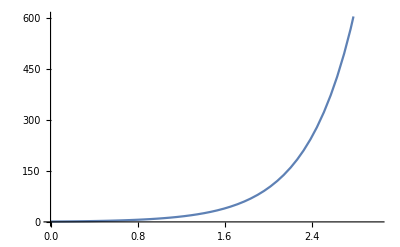

```mathematica
Plot[10^x,{x,0,3}]
```

## Manipulate로 함수 관찰하기

```mathematica
Manipulate[x^2,{x,1,10}]
```

```mathematica
Manipulate[x^2,{x,0,50,5}]
```

```mathematica
Manipulate[Plot[x Sin[1/x],{x,0,r}],{r,.1,2}]
```

```mathematica
Manipulate[Plot[x Sin[1/x],{x,0,r}],{{r,0.2,"right endpoint"},10^-10,2}]
```

```mathematica
Manipulate[Plot[x Sin[x],{x,-10,10},PlotStyle->Directive[Thickness[t],Dashing[{d}],Blend[{Red,Blue},b]]],{{t,.01,"Thickness"},.001,.02},{{d,.02,"Dash Size"},0,.04},{{b,.5,"Percent Blue"},0,1}]
```

```mathematica
Manipulate[Plot[a(x-b)^2+c,{x,-5,5},PlotRange->5,PlotLabel->"y=a(x-b)^2+c"],{a,-1,1},{{b,-1},-3,3},{{c,2},-3,3}]
```

```mathematica
Manipulate[Plot[Sin[4/x],{x,-2π,2π},PlotPoints->pp,MaxRecursion->mr,Mesh->m],{{pp,64,"PlotPoints"},{4,8,16,32,64}},{{mr,4,"MaxRecursion"},{0,1,2,3,4}},{{m,Full,"Mesh"},{Full,All,None}}]
```

```mathematica
Manipulate[Plot[f[x],{x,0,4π},Ticks->{Range[0,4π,π/2],Automatic},PlotLabel->f[x]],{{f,Tan,"function"},{Sin,Cos,Sec,Csc,Tan,Cot},ControlType->SetterBar}]
```

```mathematica
Manipulate[Plot[x Sin[x],{x,-20,20},AxesOrigin->pt,PlotRange->20],{{pt,{0,0},"Move the axes:"},{-20,20},{20,20}},ControlPlacement->Left]
```

```mathematica
Manipulate[Plot[x Sin[x],{x,-20,20},AxesOrigin->pt,PlotRange->20],{{pt,{0,0}},Locator}]
```

The iterator structure {var, colorSetting} will produce a color slider.

```mathematica
Manipulate[Plot[Sin[x]/x,{x,0,20},PlotStyle->color],{color,Blue}]
```

#### Manipulate의 매개변수로 넣을 수 있는 반복자에 그에 따른 기본 조정자

Iterator Form | Default ContrlType
{u,u_min,∞} | Animator
{u,u_min,u_max} | Manipulator
{u,u_min,u_max,du} | discrete Manipulator with step du
{u,{x_min,y_min},{x_max,y_max}} | Slider2D
{u,{x_min,y_min},{x_max,y_max},{dx,dy}} | discrete Slider2D with horizontoal step dx, vertical step dy
{u,Locator} | Locator
{u,{True,False}} | Checkbox
{u,{value_1,value_2,…}} | popupMenu (or SetterBar if fewer than 6 items)
{u,color} | ColorSlider
{u} | InputField

#### 각 반복자에 적용할 수 있는 Manipulate 조정자

Iterator Form | Valid ControlType Settings
{u,u_min,u_max} | Animator, InputField, Manipulator, Slider, Slider2D, VerticalSlider, None
{u,{x_min,y_min},{x_max,y_max}} | Animator, InputField, Manipulator, PopupMenu, RadioButtonBar, SetterBar, Slider, Slider2D, VerticalSlider, None
{u,{x_min,y_min},{x_max,y_max},{dx,dy}} | InputField, Locator, Slider2D, None
{u,Locator} | Locator, None
{u,{True,False}} | Animator, Checkbox, CheckboxBar, InputField,Manipulator, Opener,PopupMenu,RadioButtonBar,SetterBar,Slider,VerticalSlider,None
{u,{value_1,value_2,…}} | Animator,Checkbox,CheckboxBar,InputField,Manipulator,PopupMenu,RadioButtonBar,SetterBar,Slider,Togglebar,VerticalSlider,None
{u,color} | ColorSetter,ColorSlider,InputField,None
{u} | InputField,None

### 다른 동적 표현 명령어

```mathematica
OpenerView[{Style["click the triangle","Text"],Style["Hah, you did it!","Section"]}]
```

```mathematica
TabView[{"sine"->Plot[Sin[x],{x,0,2π}],"cosine"->Plot[Cos[x],{x,0,2π}]},ImageSize->Automatic]
```

12

### 바람직한 Manipulate 사용법

변수 이름은 변수의 용도를 잘 나타내도록 정한다.

자세한 지식 없이도 실행해 볼 수 있도록 초깃값을 정한다.

```mathematica
Manipulate[Plot[Sin[x],{x,0,2π},Background->RGBColor[r,g,b]],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Manipulate[Plot[Sin[x],{x,0,2π},Background->Hue[h,s,b]],{h,0,1},{{s,1},0,1},{{b,1},0,1}]
```

## 테이블 사용하기

#### 괄호의 용법

() | 연산의 우선순의 지정
[] | 함수의 매개변수 지정
{} | 리스트 정의

## 그리드 조정하기

```mathematica
Manipulate[Text@Grid[{{"x","x^2"},{x,x^2}},Dividers->All,ItemSize->5],{{x,5.3},1,10,.1}]
```

```mathematica
Manipulate[Text@Grid[{{"C","F"},{c,1.8c+32}},Dividers->All,ItemSize->5],{{c,0},-40,1000,1}]
```

## 구간별로 정의된 함수

## 음함수의 그래프

#### 등호의 용법

= | 우변의 값에 좌면의 이름을 할당(Set)
:= | 지연 할당(SetDelayed)
== | 등호(Equal)
=== | 좌우변의 표현 비교(SameQ)

## 그래프 겹쳐 그리기

### 그래프의 중첩

### 색으로 채우기

### 그래픽의 중첩

### 중첩된 그래프

### 그래픽의 나열

### 그래픽의 격자 배열

## 그래픽 다듬기

### 그리기 도구

### 기본 도형

## 자료 다루기

## 리스트

## 차분 방정식